```mathematica
Series[ArcSin[x],{x,0,3}]
```

x+x^3/6+O[x]^4

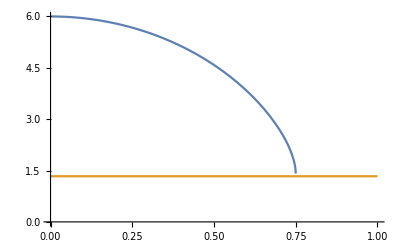

```mathematica
r=2;
n=4/3;
Plot[{-2*(1-√(1-x^2))+(r*x)/(ArcSin[n x]-ArcSin[x]),4/3},{x,0,1}, PlotRange->{Automatic, {0,6}}]
```

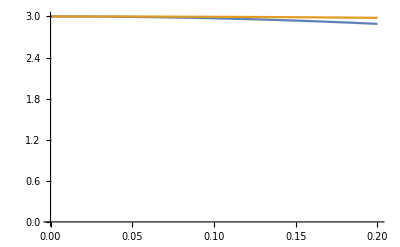

```mathematica
n=4/3;
a[d_]:=ArcSin[d];
b[d_]:=ArcSin[n d];
g[d_]:=b[d]-a[d];
x[d_]:=d/Tan[g[d]]-(1-√(1-d^2));
Plot[{x[d],1/(n-1)-d^2/2},{d,0,.2}, PlotRange->{Automatic,{ 0,3}}]
```

```mathematica
x[d]
```

-1+√(1-d^2)-d Cot[ArcSin[d]-ArcSin[(4 d)/3]]